```mathematica
Explorations in Sound
```

## Basics of Sine Waves

```mathematica
Column[{Text[Style["A",Bold,25,Red]Style["Sin(",25,Bold,Black]Style["ω",Bold,25,Purple]Style["t",25,Bold,Black]Text[Style[")",25,Bold,Black]]], 


Style["Angular Frequency",24,Bold,Purple]Text[Style["ω=2π*(frequency). Frequency controls the horizontal length between two points",20,Black]],

Text[Style[":controls the vertical length between the peaks and troughs",20,Black]]Style["Amplitude",24,Bold,Red]},Spacings->3]
```

A Sin( t ω )
Angular Frequency ω=2π*(frequency). Frequency controls the horizontal length between two points
Amplitude :controls the vertical length between the peaks and troughs

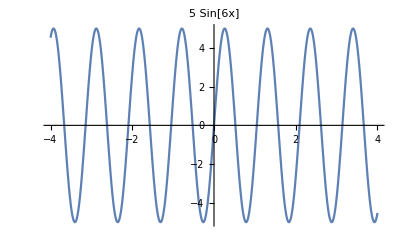

```mathematica
Plot[5Sin[6x],{x,-4,4},PlotLabel->Style["5 Sin[6x]",20,Bold,Black]]
```

```mathematica
Manipulate[{Plot[Sin[(a/400) x 2 Pi],{x,0,2Pi}],Play[Sin[a 2 Pi t],{t,0,3}]},Style["Frequency Controls Pitch",20,Bold],{{a,20,"frequency"},400,800,100},ContinuousAction->False]
```

```mathematica
Manipulate[{Sound[Play[Sin[800 2 π t],{t,0,3}],SoundVolume->a/1000],Plot[a Sin[2 Pi t],{t,0,3},PlotRange->{{0,3},{-55,55}}]},Style["Amplitude Controls Volume",20,Bold],{{a,20,"amplitude"},1,55,1}]
```

## Why do instruments playing the same note sound different?

Most sounds are not just simple Sine waves, but instead much more complex waves

But notice that the wave is still periodic. There’s a pattern that repeats over and over.

Joseph Fourier made an incredible discovery: any periodic function you can think of, no matter how crazy, can be represented by a sum of simple sines and cosines

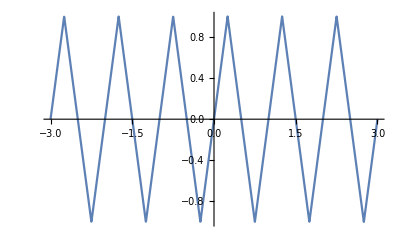

```mathematica
Plot[TriangleWave[x],{x,-3,3}]
```

```mathematica
FourierSinSeries[TriangleWave[x],x,10,FourierParameters->{1,2Pi}]
```

(8 Sin[2 π x])/π^2-(8 Sin[6 π x])/(9 π^2)+(8 Sin[10 π x])/(25 π^2)-(8 Sin[14 π x])/(49 π^2)+(8 Sin[18 π x])/(81 π^2)

```mathematica
Manipulate[Plot[{(8 Sin[2 π x] Subscript[a, 1])/π^2-(8 Sin[6 π x] Subscript[a, 2])/(9 π^2)+(8 Sin[10 π x] Subscript[a, 3])/(25 π^2)-(8 Sin[14 π x] Subscript[a, 4])/(49 π^2)+(8 Sin[18 π x] Subscript[a, 5])/(81 π^2)},{x,-2,2},PlotRange->{{-2,2},{-1,1}}],Style["Ingredients of a Triangle Wave",20,Bold,Blue],{{Subscript[a, 1],20,"Wave1"},0,1},{{Subscript[a, 2],20,"Wave2"},0,1},{{Subscript[a, 3],20,"Wave3"},0,1},{{Subscript[a, 4],20,"Wave4"},0,1},{{Subscript[a, 5],20,"Wave5"},0,1}]
```

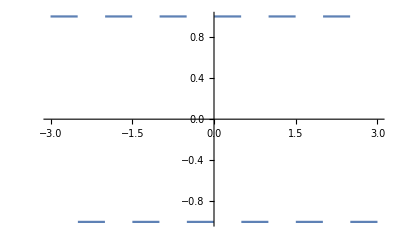

```mathematica
Plot[SquareWave[x],{x,-3,3}]
```

```mathematica
FourierSinSeries[SquareWave[x],x,10,FourierParameters->{1,2Pi}]
```

(4 Sin[2 π x])/π+(4 Sin[6 π x])/(3 π)+(4 Sin[10 π x])/(5 π)+(4 Sin[14 π x])/(7 π)+(4 Sin[18 π x])/(9 π)

```mathematica
Manipulate[Plot[{(1/2)+(2/Pi)(Sin[x] Subscript[a, 1]+1/3 Sin[3 x] Subscript[a, 3]+1/5 Sin[5 x] Subscript[a, 5]+1/7 Sin[7 x] Subscript[a, 7]+1/9 Sin[9 x] Subscript[a, 9]+1/11 Sin[11 x] Subscript[a, 11])},{x,0,12},PlotRange->{{0,12},{-10,10}}],Style["Ingredients of a Square Wave",20,Bold,Blue],{{Subscript[a, 1],20,"Wave1"},0,10},{{Subscript[a, 3],20,"Wave2"},0,10},{{Subscript[a, 5],20,"Wave3"},0,10},{{Subscript[a, 7],20,"Wave4"},0,10},{{Subscript[a, 9],20,"Wave5"},0,10},{{Subscript[a, 11],20,"Wave6"},0,10}]
```

#### Press Each Button to Hear the Different Sounds

```mathematica
{Button["Sine Wave",EmitSound[Play[Sin[2750x],{x,0,1.5}]]],Button["Square Wave",EmitSound[Play[SquareWave[440 x],{x,0,1.5}]]],Button["Triangle Wave",EmitSound[Play[TriangleWave[440 x],{x,0,1.5}]]]}
```

{Sine Wave,Square Wave,Triangle Wave}

## Fourier Analysis (Working Progress)

```mathematica
(*The ultimate goal is create a module that shows students how they can import any sound, perform fourier function on it, and be able to recreate that noice by adding periodic functions together*)
(*The following code is ways that I was exploring to see if that is possible, still working on it*)
Import["C:\\Users\\Jesse Heidohrn\\Downloads\\Piano note comparison - Middle C 6 Mic Perspectives.mp3"]
```

```mathematica
AudioTrim[,3]
```

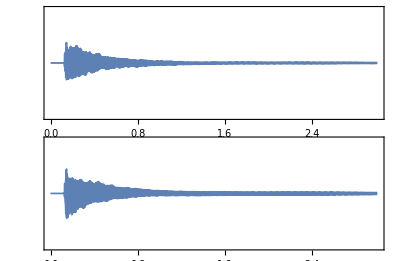

```mathematica
AudioPlot[]
```

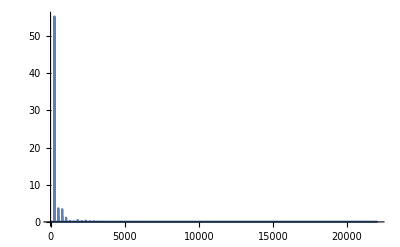
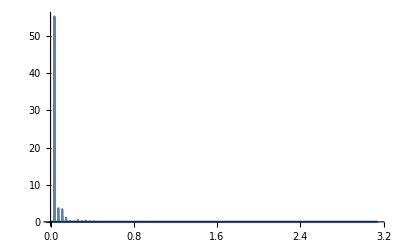

```mathematica
Periodogram[,DataRange->#, ScalingFunctions->"Absolute",PlotRange->All]&/@{Automatic,{0, Pi}}
```

```mathematica
AudioData[]//Short
```

{{0.,-7.76527×10^-16,«132296»,-0.0105551,-0.0105765},«1»}

```mathematica
Flatten[%91]
```

{0.,-7.76527×10^-16,6.14493×10^-16,1.00868×10^-15,9.55348×10^-17,-1.57205×10^-15,-1.15658×10^-15,264586,-0.0125851,-0.0131961,-0.0137686,-0.0143489,-0.0149011,-0.015371,-0.0158366}
 |  |  |  |

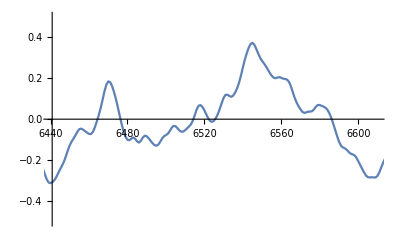

```mathematica
ListLinePlot[%[[;;50000]],PlotRange->{{6440,6610},{-.5,.5}}]
```

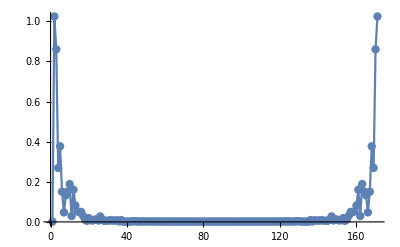

```mathematica
ListLinePlot[%97,Mesh->All,PlotRange->All]
```

```mathematica
FindPeaks[a,10]
```

{{2,1.02396},{171,1.02396}}

## The Doppler Effect

An interesting effect of waves being produced by a source in motion relative to an observer

```mathematica
Style["f=((c + SubscriptBox[v, o])/(c + SubscriptBox[v, s]))f_0",20,Bold,Black]
```

f=((c + SubscriptBox[v, o])/(c + SubscriptBox[v, s]))f_0

```mathematica
Style["c=speed of wave in medium",18,Bold,Black]
Style["v_o=velocity of observer",18,Bold,Black]
Style["v_s=velocity of source",18,Bold,Black]
Style["f_0=frequency emitted by source",18,Bold,Black]
Style["f=frequency observed",18,Bold,Black]
```

c=speed of wave in medium
"v_o=velocity of observer"
"v_s=velocity of source"
"f_0=frequency emitted by source"
f=frequency observed

```mathematica
Manipulate[{Play[Sin[(340.29/(340.29+v((90-v x)/Sqrt[d^2+(90-v x)^2])))^-1 2 Pi f x],{x,0,6}],{Animate[{Graphics[{Circle[{-10,-d},2],Blue,Dashed,Line[{{-100,0},{80,0}}],Red,Scale[Disk[{-100.+v t,5},.35],5],Blue,Scale[Polygon[{{-102.6+v t,0},{-102.5+v t,1},{-101.8+v t,1},{-101.6+v t,1.7},{-99.6+v t,1.7},{-99.39999999999999+v t,1},{-98.6+v t,0.9},{-98.6+v t,0},{-102.6+v t,0}}],5],LightBlue,Scale[Polygon[{{-101.8+v t,3},{-101.6+v t,3.7},{-99.6+v t,3.7},{-99.39999999999999+v t,3}}],4],Black,Scale[Disk[{-98+v t,3.7},0.3],5],GrayLevel[0],Scale[Disk[{-104.6+v t,-3},.5],5],Scale[Disk[{-95.6+v t,-3},.5],5],GrayLevel[.5],Scale[Disk[{-104.6+v t,-3},0.25],5],Scale[Disk[{-95.6+v t,-3},0.25],5]},PlotRange->{{-70,40},{10,-32}},ImageSize->Large]},{t,-4,6},AnimationRepetitions->1,AnimationRunning->False]}},{{d,20,"observer location"},0,30,1},{{f,20,"frequency emitted"},400,1100,100},{{v,20,"velocity of emitter"},25,55,1},ContinuousAction->False,SaveDefinitions->True]
```